```mathematica
Manipulate[
Module[{t,w,L,P,Ac,k,u,ν,ρ,μ,ka,Cp,Pr,Rex,h,Tb,m,qf,T,col,rectangular,pin},
(*size stuff*)
t=0.0015;(*m*)
w=0.02;
L:=length/1000;

If[fin==1,
{P:=2*w+2*t;Ac:=w*t;},
{P:=π*t;Ac:=π*(t/2)^2;}];

(*therm. data*)
k:=Which[
mat==1,14,(*s.steel*)
mat==2,60.5,(*carbon steel*)
mat==3,80.2,(*iron*)
mat==4,110,(*brass*)
mat==5,237,(*aluminum*)
mat==6,401(*copper*)
];(*W/m/K*)

(*air properties*)
u=2;(*m/s*)
ν=1.71*^-5;(*m2/s*)
ρ=1.164;(*kg/m3*)
μ:=ν*ρ;(*N s/m2*)
ka=0.0264;(*W/m/K*)
Cp=1005;(*J/kg/K*)

Pr:=(Cp*μ)/ka;
Rex:=(u*If[fin==1,w,t])/ν;
h:=If[fin==1,
ka/w*0.664*Rex^(1/2)*Pr^(1/3),
If[Rex<4000,ka/t*0.683*Rex^0.466*Pr^(1/3),ka/t*0.193*Rex^0.618*Pr^(1/3)]
];

(*heat, temperature*)
Tb=500;(*K*)
m:=√((2*h)/(k*t));
qf:=(Tb-Ta)*√(h*P*k*Ac)*Tanh[m*L];
T[x_]:=(Tb-Ta)*Cosh[m*(L-x)]/Cosh[m*L]+Ta;

(*Plot[T[x],{x,0,L},PlotStyle->{Thick,Black},Frame->True,PlotRange->{300,500},PlotRangePadding->{None,5}]*)

col[x_]:=ColorData["TemperatureMap"][Rescale[T[x],{If[fin==1,386.5,307.3],Tb}]];

rectangular:=Show[
Graphics3D[{col[0],Cuboid[{-0.0025,-w/2,-w/2},{0,w/2,w/2}]}],
RegionPlot3D[z<t,{x,0,L},{y,-w/2,w/2},{z,0,t},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False]
];

pin:=Show[
Graphics3D[{{col[0],Cuboid[{-0.0025,-w/2,-w/2},{0,w/2,w/2}]},{col[L],Cylinder[{{0.999*L,0,0},{L,0,0}},t/2]}}],
ParametricPlot3D[{x,t/2*Sin[θ],t/2*Cos[θ]},{θ,0,2*π},{x,0,L},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False]
];

(*Show[Switch[fin,1,rectangular,2,pin],Boxed->False,ViewPoint->{2,-2,1},Lighting->"Neutral",ImageSize->{300,350}]*)
Plot[x,{x,0,L},Filling->0,ColorFunction->(col[#1]&),ColorFunctionScaling->False]
],
Column[{
Row[{
Control[{{fin,1,"fin type:"},{1->" rectangular ",2->" pin "},Setter}],Spacer[20],
Control[{{mat,1,"material:"},{1->"stainless steel",2->"carbon steel",3->"iron",4->"brass",5->"aluminum",6->"copper"},PopupMenu}]
}],
Control[{{length,10,"fin length (mm)"},5,20,1,Appearance->"Labeled"}],
Control[{{Ta,300,"ambient temperature (K)"},250,350,1,Appearance->"Labeled"}]
}]
]
```

```mathematica
(*ν:=9*^-11*Ta^2+4*^-8*Ta-3*10^-6;
ρ:=313.43*Ta^-0.981;
μ:=ν*ρ;
ka:=-2*^-8*Ta^2+9*^-5*Ta+0.0012;*)
```

```mathematica
386.5
307.3
```

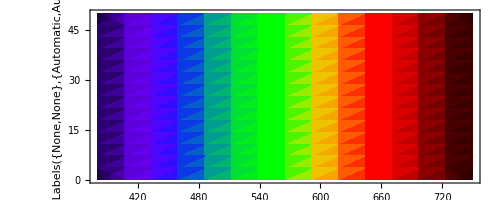

```mathematica
DensityPlot[
x,{x,380,750},{y,0,50},
ColorFunction->ColorData["VisibleSpectrum"],
ColorFunctionScaling->False,
AspectRatio->Automatic,
PlotRangePadding->10]
```

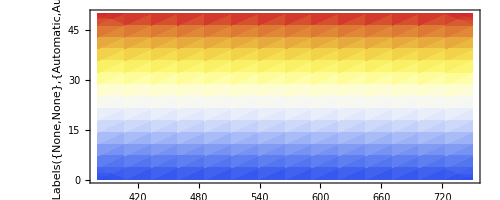

```mathematica
DensityPlot[
y,{x,380,750},{y,0,50},
ColorFunction->ColorData["TemperatureMap"],
(*ColorFunctionScaling->False,*)
AspectRatio->Automatic,
PlotRangePadding->10]
```

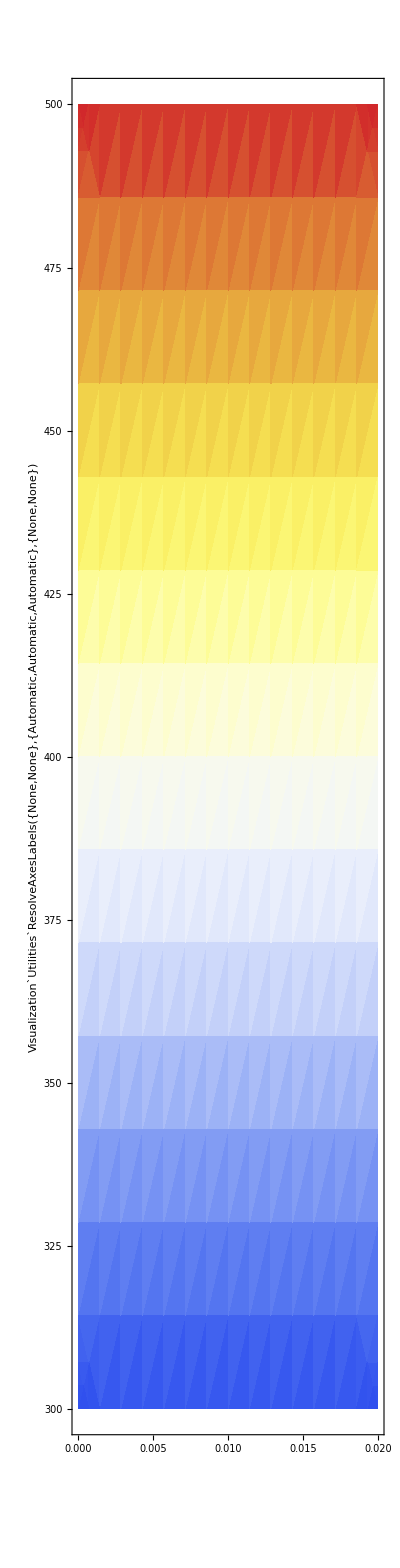

```mathematica
DensityPlot[y,{x,0,0.02},{y,300,500},
ColorFunction->ColorData["TemperatureMap"],
AspectRatio->5]
```

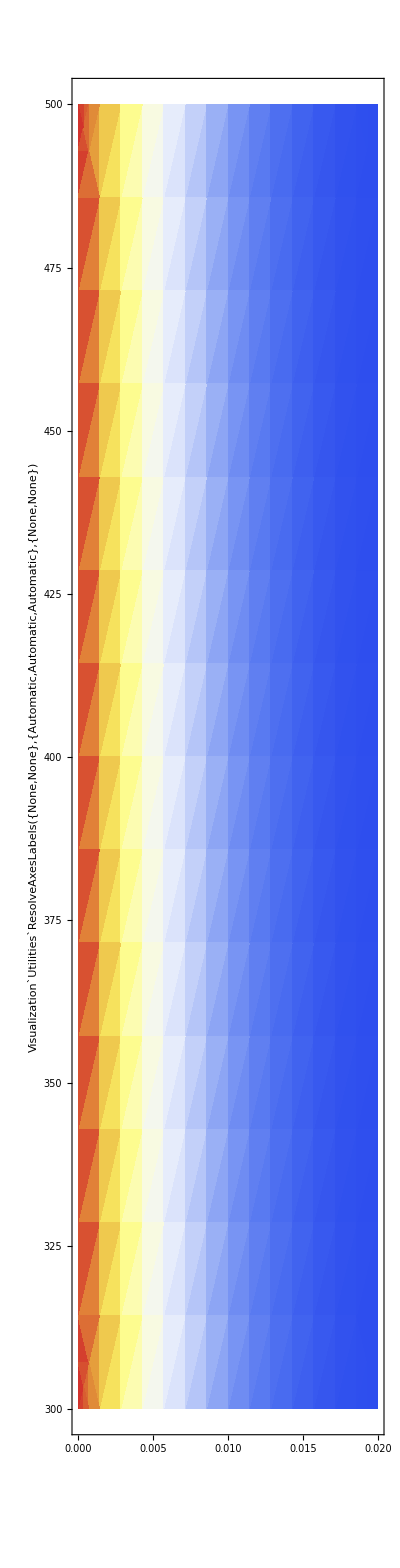

```mathematica
Module[{Tx,xT},
Tx[x_]:=250*(1+0.229*Cosh[107.7*(0.02-x)]);
xT:=Interpolation[Table[{t,x/.FindRoot[Tx[x]==t,{x,0}]},{t,307.3,500}]];

(*DensityPlot[Tx[y],{x,300,500},{y,0,0.02},
ColorFunction->ColorData["TemperatureMap"],
AspectRatio->5]*)

DensityPlot[Tx[y],{y,0,0.02},{x,300,500},
ColorFunction->ColorData["TemperatureMap"],
AspectRatio->5]
]
```

```mathematica
Module[{Tb,TL,T},
Tb=500;
TL:=T[0.02];
T[x_]:=250*(1+0.229*Cosh[107.7*(0.02-x)]);

Plot[Tb,{x,0,0.02},
ColorFunction->(ColorData["TemperatureMap"][#2]&),
(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#2,{TL,Tb}]]&),*)
ColorFunctionScaling->False,
Filling->T[0.02],
PlotRange->{{0,0.02},{T[0.02],Tb}},
AspectRatio->5,
ImageSize->100]
]
```

-Graphics-

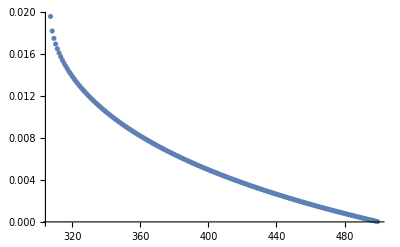

```mathematica
Module[{L1,f1},
L1:=Table[{t,x/.FindRoot[250*(1+0.229*Cosh[107.7*(0.02-x)])==t,{x,0}]},{t,307.3,500}];
f1:=Interpolation[L1];

]
```

```mathematica
250*(1+0.229*Cosh[107.7*(0.02-x)])/.x->0.02
```

307.25

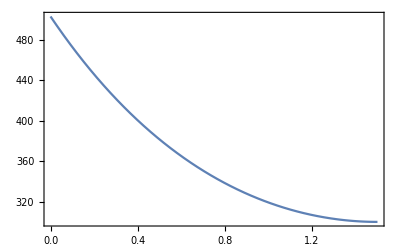

```mathematica
Plot[150*(1+Cosh[1.5-x]),{x,0,1.5},Frame->True]
```

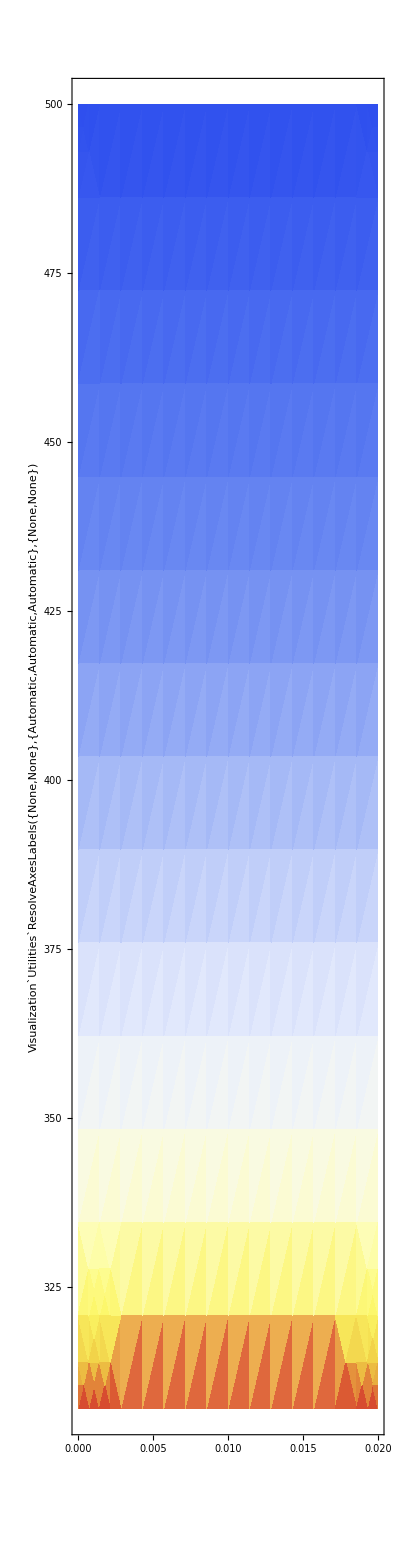

```mathematica
Module[{Tx,xT},
Tx[x_]:=250*(1+0.229*Cosh[107.7*(0.02-x)]);
xT:=Evaluate@Quiet@Interpolation[Table[{t,x/.FindRoot[Tx[x]==t,{x,0}]},{t,500,307,-1}]];

(*DensityPlot[xT[y],{x,0,0.02},{y,307,500},
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
AspectRatio->5]*)

DensityPlot[xT[y],{x,0,0.02},{y,307,500},
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
AspectRatio->5]
]
```

```mathematica
Module[{Tx,xT},
Tx[x_]:=250*(1+0.229*Cosh[107.7*(0.02-x)]);
xT:=Quiet@Table[{t,x/.FindRoot[Tx[x]==t,{x,0}]},{t,307,500}];

xT
]
```

{{307,0.02},{308,0.0184987},{309,0.01771},{310,0.0171335},{311,0.0166574},{312,0.0162434},{313,0.0158726},{314,0.0155343},{315,0.0152216},{316,0.0149297},{317,0.0146552},{318,0.0143954},{319,0.0141485},{320,0.0139128},{321,0.0136871},{322,0.0134703},{323,0.0132615},{324,0.01306},{325,0.0128653},{326,0.0126766},{327,0.0124936},{328,0.0123158},{329,0.0121429},{330,0.0119746},{331,0.0118105},{332,0.0116504},{333,0.0114941},{334,0.0113414},{335,0.011192},{336,0.0110457},{337,0.0109025},{338,0.0107622},{339,0.0106246},{340,0.0104897},{341,0.0103572},{342,0.0102271},{343,0.0100993},{344,0.00997369},{345,0.00985019},{346,0.00972871},{347,0.00960918},{348,0.00949153},{349,0.00937569},{350,0.00926159},{351,0.00914918},{352,0.00903839},{353,0.00892918},{354,0.0088215},{355,0.00871529},{356,0.0086105},{357,0.00850711},{358,0.00840506},{359,0.00830432},{360,0.00820484},{361,0.0081066},{362,0.00800956},{363,0.00791368},{364,0.00781893},{365,0.0077253},{366,0.00763273},{367,0.00754122},{368,0.00745073},{369,0.00736124},{370,0.00727272},{371,0.00718515},{372,0.00709851},{373,0.00701277},{374,0.00692792},{375,0.00684393},{376,0.00676079},{377,0.00667848},{378,0.00659698},{379,0.00651627},{380,0.00643633},{381,0.00635716},{382,0.00627872},{383,0.00620102},{384,0.00612403},{385,0.00604774},{386,0.00597213},{387,0.0058972},{388,0.00582293},{389,0.00574931},{390,0.00567632},{391,0.00560395},{392,0.0055322},{393,0.00546104},{394,0.00539048},{395,0.00532049},{396,0.00525108},{397,0.00518223},{398,0.00511392},{399,0.00504616},{400,0.00497892},{401,0.00491221},{402,0.00484602},{403,0.00478033},{404,0.00471513},{405,0.00465043},{406,0.00458621},{407,0.00452246},{408,0.00445918},{409,0.00439636},{410,0.00433399},{411,0.00427206},{412,0.00421058},{413,0.00414952},{414,0.00408889},{415,0.00402869},{416,0.00396889},{417,0.0039095},{418,0.00385052},{419,0.00379193},{420,0.00373373},{421,0.00367591},{422,0.00361848},{423,0.00356142},{424,0.00350473},{425,0.0034484},{426,0.00339243},{427,0.00333682},{428,0.00328155},{429,0.00322664},{430,0.00317206},{431,0.00311782},{432,0.00306391},{433,0.00301032},{434,0.00295707},{435,0.00290413},{436,0.0028515},{437,0.00279919},{438,0.00274719},{439,0.00269549},{440,0.00264409},{441,0.00259299},{442,0.00254218},{443,0.00249166},{444,0.00244142},{445,0.00239147},{446,0.0023418},{447,0.00229241},{448,0.00224328},{449,0.00219443},{450,0.00214585},{451,0.00209752},{452,0.00204946},{453,0.00200166},{454,0.00195411},{455,0.00190682},{456,0.00185977},{457,0.00181298},{458,0.00176642},{459,0.00172011},{460,0.00167403},{461,0.0016282},{462,0.00158259},{463,0.00153722},{464,0.00149208},{465,0.00144716},{466,0.00140247},{467,0.001358},{468,0.00131375},{469,0.00126972},{470,0.0012259},{471,0.00118229},{472,0.0011389},{473,0.00109572},{474,0.00105274},{475,0.00100997},{476,0.000967395},{477,0.000925026},{478,0.000882855},{479,0.000840881},{480,0.000799103},{481,0.000757517},{482,0.000716123},{483,0.000674919},{484,0.000633902},{485,0.000593072},{486,0.000552425},{487,0.000511961},{488,0.000471679},{489,0.000431575},{490,0.000391649},{491,0.000351899},{492,0.000312323},{493,0.000272921},{494,0.000233689},{495,0.000194628},{496,0.000155734},{497,0.000117008},{498,0.0000784464},{499,0.0000400491},{500,1.81422×10^-6}}

```mathematica
Table[t,{t,500,300,-10}]
```

{500,490,480,470,460,450,440,430,420,410,400,390,380,370,360,350,340,330,320,310,300}

```mathematica
Module[{Tx,xT},
Tx[x_]:=250*(1+0.229*Cosh[107.7*(0.02-x)]);
xT:=Evaluate@Quiet@Interpolation[Table[{t,x/.FindRoot[Tx[x]==t,{x,0}]},{t,500,307,-1}]];

DensityPlot[500,{x,0,0.02},{y,307,500},
ColorFunction->Function[{x,y},ColorData["TemperatureMap"][xT[y]]],
(*ColorFunction->(ColorData["TemperatureMap"][xT[#1]]&),*)
ColorFunctionScaling->True,
AspectRatio->5]

]
```

-Graphics-

```mathematica
Module[{T,xT},
T[x_]:=250*(1+0.229*Cosh[107.7*(0.02-x)]);
xT:=Evaluate@Quiet@Interpolation[Table[{500-t,x/.FindRoot[T[x]==300+t,{x,0}]},{t,0,200}]];

BarLegend[{ColorData["TemperatureMap"][Rescale[xT[#],{0,0.02}]]&,{300,500}}]
]
```